## Function Definitions

Don’t forget that there’s also an omega floating around

### For m = 0

```mathematica
const1=1/(2*Pi)
```

1/(2 π)

```mathematica
p0[e_,s_]:=const1*Integrate[Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

```mathematica
Np0[e_,s_]:=const1*NIntegrate[Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi}]
```

```mathematica
p0NoPole[e_,s_]:=const1*Integrate[(1-e^2)^(3/2)*Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi},Assumptions->{e≥0,e≤1,Element[s,Integers]}]
```

```mathematica
Np0NoPole[e_,s_]:=const1*NIntegrate[(1-e^2)^(3/2)*Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi}]
```

### For m = 2

There’s also an Exp[phi_not]
Apparently that’s actually handled in POET, never mind

```mathematica
const2=1
```

1

#### Sub integrals

Symbolic integration

```mathematica
pTwoA[e_,s_]:=const1*(1-e^2)*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4),{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

```mathematica
pTwoB[e_,s_]:=const1*(1-e^2)*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Cos[2*u],{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

```mathematica
pTwoC[e_,s_]:=const1*I*Sqrt[(1-e^2)]*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[2*u],{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

```mathematica
pTwoD[e_,s_]:=const1*I*2*e*Sqrt[(1-e^2)]*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[u],{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

Numeric integration

```mathematica
NpTwoA[e_,s_]:=const1*(1-e^2)*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4),{u,0,2*Pi}]
```

```mathematica
NpTwoB[e_,s_]:=const1*(1-e^2)*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Cos[2*u],{u,0,2*Pi}]
```

```mathematica
NpTwoC[e_,s_]:=const1*I*Sqrt[(1-e^2)]*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[2*u],{u,0,2*Pi}]
```

```mathematica
NpTwoD[e_,s_]:=const1*I*2*e*Sqrt[(1-e^2)]*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[u],{u,0,2*Pi}]
```

#### Main Coefficients

I’m not sure why I’m dividing by const1, but I don’t believe it’s causing any issues w/ regard to behavior, so I’m just going to leave it for now
10/9/2020 got rid of const1 b/c it was causing issues w/ regard to behavior

Symbolic

```mathematica
pPlus2[e_,s_]:=(1/(1*const2))*(p0[e,s]-pTwoA[e,s]+pTwoB[e,s]-pTwoC[e,s]+pTwoD[e,s])
```

```mathematica
pMinus2[e_,s_]:=(const2/1)*(p0[e,s]-pTwoA[e,s]+pTwoB[e,s]+pTwoC[e,s]-pTwoD[e,s])
```

```mathematica
pPlus2Ltd[e_,s_]:=(1/(1*const2))*(0-pTwoA[e,s]+pTwoB[e,s]-pTwoC[e,s]+pTwoD[e,s])
```

```mathematica
pMinus2Ltd[e_,s_]:=(const2/1)*(0-pTwoA[e,s]+pTwoB[e,s]+pTwoC[e,s]-pTwoD[e,s])
```

```mathematica
pPlus2NP[e_,s_]:=((1-e^2)^(3/2)/(1*const2))*(p0[e,s]-pTwoA[e,s]+pTwoB[e,s]-pTwoC[e,s]+pTwoD[e,s])
```

```mathematica
pMinus2NP[e_,s_]:=(1-e^2)^(3/2)*(const2/1)*(p0[e,s]-pTwoA[e,s]+pTwoB[e,s]+pTwoC[e,s]-pTwoD[e,s])
```

Numeric

```mathematica
NpPlus2[e_,s_]:=(1/(1*const2))*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]-NpTwoC[e,s]+NpTwoD[e,s])
```

```mathematica
NpMinus2[e_,s_]:=(const2/1)*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]+NpTwoC[e,s]-NpTwoD[e,s])
```

```mathematica
NpPlus2Ltd[e_,s_]:=(1/(1*const2))*(0-NpTwoA[e,s]+NpTwoB[e,s]-NpTwoC[e,s]+NpTwoD[e,s])
```

```mathematica
NpMinus2Ltd[e_,s_]:=(const2/1)*(0-NpTwoA[e,s]+NpTwoB[e,s]+NpTwoC[e,s]-NpTwoD[e,s])
```

```mathematica
NpPlus2NP[e_,s_]:=((1-e^2)^(3/2)/(1*const2))*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]-NpTwoC[e,s]+NpTwoD[e,s])
```

```mathematica
NpMinus2NP[e_,s_]:=((1-e^2)^(3/2))*(const2/1)*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]+NpTwoC[e,s]-NpTwoD[e,s])
```

```mathematica
NpPlus2NPLtd[e_,s_]:=((1-e^2)^(3/2)/(1*const2))*(0-NpTwoA[e,s]+NpTwoB[e,s]-NpTwoC[e,s]+NpTwoD[e,s])
```

```mathematica
NpMinus2NPLtd[e_,s_]:=((1-e^2)^(3/2))*(const2/1)*(0-NpTwoA[e,s]+NpTwoB[e,s]+NpTwoC[e,s]-NpTwoD[e,s])
```

## Verifying Values

```mathematica
p0[e,0]
```

ConditionalExpression[1/((1-e^2)^(3/2)),e<1]

```mathematica
p0NoPole[e,0]
```

ConditionalExpression[1,0<e<1]

```mathematica
pPlus2[e,0]
```

ConditionalExpression[(5 e^2)/(2 (1-e^2)^(5/2))+1/((1-e^2)^(3/2))-(2+3 e^2)/(2 (1-e^2)^(5/2)),e<1]

```mathematica
FullSimplify[ConditionalExpression[2 ((5 e^2)/(2 (1-e^2)^(5/2))+1/((1-e^2)^(3/2))-(2+3 e^2)/(2 (1-e^2)^(5/2))) ⅇ^(-2 ⅈ) π,0<e<1]]
```

ConditionalExpression[0,0<e<1]

```mathematica
FullSimplify[pMinus2[e,0]]
```

ConditionalExpression[0,e<1]

## p_0s behavior

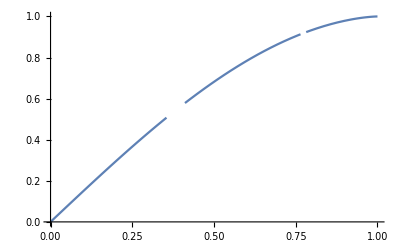

```mathematica
Plot[Np0NoPole[e,1],{e,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.1269×10^-7}. NIntegrate obtained -6.59195×10^-16 + 4.16334×10^-16\ ⅈ and 1.50742×10^-12 for the integral and error estimates.

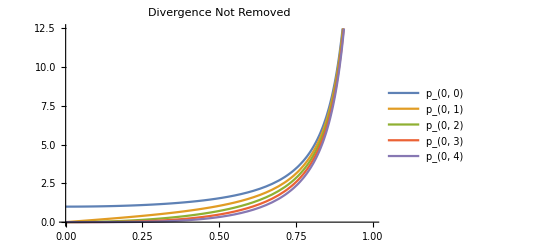

```mathematica
Plot[{Re[Np0[e,0]],Re[Np0[e,1]],Re[Np0[e,2]],Re[Np0[e,3]],Re[Np0[e,4]]},{e,0,1},PlotLegends->{"p_(0, 0)","p_(0, 1)","p_(0, 2)","p_(0, 3)","p_(0, 4)"},PlotLabel->"Divergence Not Removed"]
```

```mathematica
FullSimplify[Series[2*Pi*p0[e,1]*((1-e^2)^(3/2)),{e,0,10}]]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^2 does not converge on {0, 2\ π}.

3 π e-(9 π e^3)/8+(9 π e^5)/64-(19 π e^7)/3072-(133 π e^9)/81920+O[e]^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.1269×10^-7}. NIntegrate obtained 1.76553×10^-13 + 6.93889×10^-16\ ⅈ and 1.36776×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.70002}. NIntegrate obtained -6.52256×10^-16 - 2.94036×10^-16\ ⅈ and 1.14334×10^-15 for the integral and error estimates.

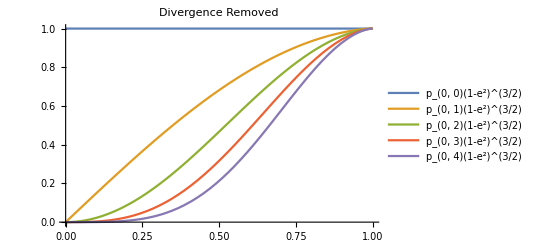

```mathematica
Plot[{Re[Np0NoPole[e,0]],Re[Np0NoPole[e,1]],Re[Np0NoPole[e,2]],Re[Np0NoPole[e,3]],Re[Np0NoPole[e,4]]},{e,0,1},PlotLegends->{"p_(0, 0)(1-e^2)^(3/2)","p_(0, 1)(1-e^2)^(3/2)","p_(0, 2)(1-e^2)^(3/2)","p_(0, 3)(1-e^2)^(3/2)","p_(0, 4)(1-e^2)^(3/2)"},PlotLabel->"Divergence Removed"]
```

#### Chebysehv

I mean, if it does work well then that will be convenient later

```mathematica
Zc1=Table[Re[2/π*(NIntegrate[Np0NoPole[x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->2]-NIntegrate[Np0NoPole[-x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->2])],{n,0,10}]
```

NIntegrate::inumr: The integrand ⅇ^ⅈ\ (u - x\ Sin[u])\ (1 - x^2)^3/2/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999998148123782572526190025430478831858227550810624961741268635}. NIntegrate obtained -0.00043738 + 4.11276×10^-15\ ⅈ and 7.01219×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.99999998148123782572526190025430478831858227550810624961741268635}. NIntegrate obtained 0.00043738  - 4.11276×10^-15\ ⅈ and 7.01219×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999998118326507805163705891701481261180095572171921958215534687}. NIntegrate obtained -0.000229582 + 7.69454×10^-15\ ⅈ and 4.84351×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{-1.41358×10^-16,1.11858,-3.53395×10^-17,-0.121053,-1.76697×10^-17,0.00318404,-1.76697×10^-17,-0.000556889,-3.97569×10^-17,-0.000292313,1.76697×10^-17}

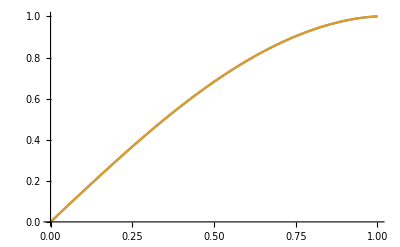

```mathematica
Plot[ {Re[Np0NoPole[x,1]],-First[Zc1]/2+Evaluate[Zc1 . Table[ChebyshevT[n-1,x],{n,Length[Zc1]}]]},{x,0,1}]
```

```mathematica
Zc2=Table[Re[2/π*(NIntegrate[Np0NoPole[x,2]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->2]-NIntegrate[Np0NoPole[-x,2]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->2])],{n,0,10}]
```

NIntegrate::inumr: The integrand ⅇ^2\ ⅈ\ (u - x\ Sin[u])\ (1 - x^2)^3/2/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999998148123782572526190025430478831858227550810624961741268635}. NIntegrate obtained -0.000593899 - 9.94799×10^-16\ ⅈ and 7.03315×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.99999998148123782572526190025430478831858227550810624961741268635}. NIntegrate obtained -0.000593899 - 9.94799×10^-16\ ⅈ and 7.03315×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999998118326507805163705891701481261180095572171921958215534687}. NIntegrate obtained -0.000226731 - 7.91001×10^-16\ ⅈ and 6.87885×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{-7.0679×10^-17,1.02841,0.,0.0302962,0.,-0.0760468,-1.76697×10^-17,0.0242917,1.76697×10^-17,-0.00991126,0.}

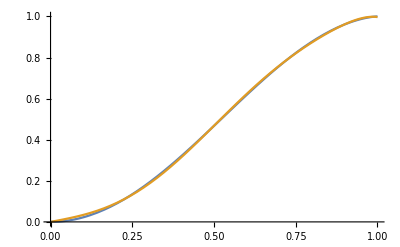

```mathematica
Plot[ {Re[Np0NoPole[x,2]],-First[Zc2]/2+Evaluate[Zc2 . Table[ChebyshevT[n-1,x],{n,Length[Zc2]}]]},{x,0,1}]
```

## p_+/-2s behavior

## What do these things do without the p_0s?

i did not make a mistake i thought i made, sweet

### W/o the factor

hi

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {5.32588}. NIntegrate obtained 4.84522×10^-13 + 2.18575×10^-16\ ⅈ and 1.04604×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

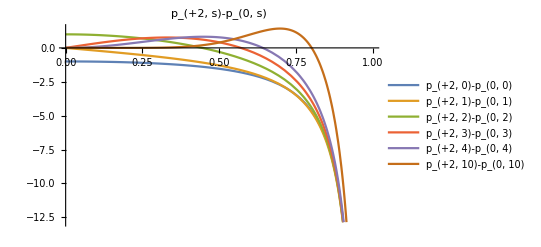

```mathematica
Plot[{Re[NpPlus2Ltd[e,0]],Re[NpPlus2Ltd[e,1]],Re[NpPlus2Ltd[e,2]],Re[NpPlus2Ltd[e,3]],Re[NpPlus2Ltd[e,4]],Re[NpPlus2Ltd[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)-p_(0, 0)","p_(+2, 1)-p_(0, 1)","p_(+2, 2)-p_(0, 2)","p_(+2, 3)-p_(0, 3)","p_(+2, 4)-p_(0, 4)","p_(+2, 10)-p_(0, 10)"},PlotLabel->"p_(+2, s)-p_(0, s)"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {5.32588}. NIntegrate obtained 4.84522×10^-13 + 2.18575×10^-16\ ⅈ and 1.04604×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

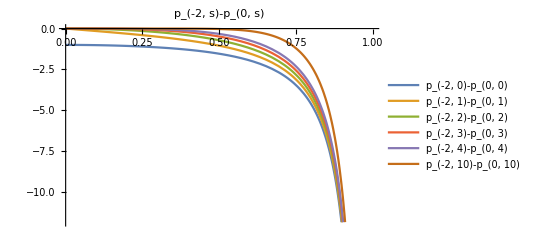

```mathematica
Plot[{Re[NpMinus2Ltd[e,0]],Re[NpMinus2Ltd[e,1]],Re[NpMinus2Ltd[e,2]],Re[NpMinus2Ltd[e,3]],Re[NpMinus2Ltd[e,4]],Re[NpMinus2Ltd[e,10]]},{e,0,1},PlotLegends->{"p_(-2, 0)-p_(0, 0)","p_(-2, 1)-p_(0, 1)","p_(-2, 2)-p_(0, 2)","p_(-2, 3)-p_(0, 3)","p_(-2, 4)-p_(0, 4)","p_(-2, 10)-p_(0, 10)"},PlotLabel->"p_(-2, s)-p_(0, s)"]
```

### W/ the factor

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {5.32588}. NIntegrate obtained 4.84522×10^-13 + 2.18575×10^-16\ ⅈ and 1.04604×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

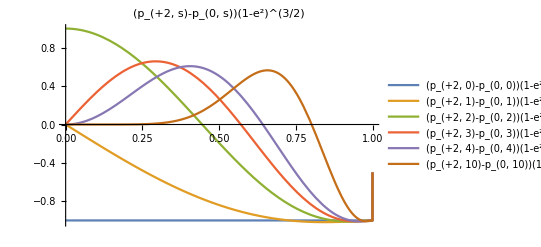

```mathematica
Plot[{Re[NpPlus2NPLtd[e,0]],Re[NpPlus2NPLtd[e,1]],Re[NpPlus2NPLtd[e,2]],Re[NpPlus2NPLtd[e,3]],Re[NpPlus2NPLtd[e,4]],Re[NpPlus2NPLtd[e,10]]},{e,0,1},PlotLegends->{"(p_(+2, 0)-p_(0, 0))(1-e^2)^(3/2)","(p_(+2, 1)-p_(0, 1))(1-e^2)^(3/2)","(p_(+2, 2)-p_(0, 2))(1-e^2)^(3/2)","(p_(+2, 3)-p_(0, 3))(1-e^2)^(3/2)","(p_(+2, 4)-p_(0, 4))(1-e^2)^(3/2)","(p_(+2, 10)-p_(0, 10))(1-e^2)^(3/2)"},PlotLabel->"(p_(+2, s)-p_(0, s))(1-e^2)^(3/2)"]
```

```mathematica
FullSimplify[(pPlus2[e,0]-(1/(const1*const2))*p0[e,0])*(1-e^2)^(3/2)]
```

ConditionalExpression[-2 π,e<1]

So yes, they do just equal -2Pi, which of course they needed to in order to cancel out p_0s.

```mathematica
FullSimplify[(pPlus2[e,1]-(1/(const1*const2))*p0[e,1])*(1-e^2)^(3/2)]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^2 does not converge on {0, 2\ π}.

```mathematica
FullSimplify[pPlus2[e,0]]
```

ConditionalExpression[0,e<1]

```mathematica
FullSimplify[pPlus2Ltd[e,0]]
```

ConditionalExpression[-(2 π)/((1-e^2)^(3/2)),e<1]

```mathematica
FullSimplify[Series[(pPlus2Ltd[e,1])*(1-e^2)^(3/2),{e,0,5}]]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^4 does not converge on {0, 2\ π}.

What about the negatives? Probably.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {5.32588}. NIntegrate obtained 4.84522×10^-13 + 2.18575×10^-16\ ⅈ and 1.04604×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

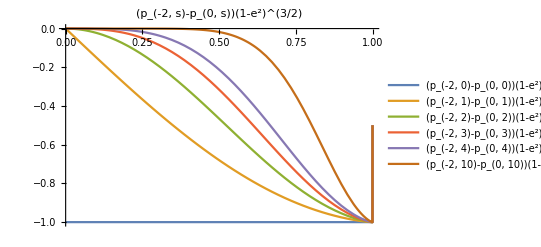

```mathematica
Plot[{Re[NpMinus2NPLtd[e,0]],Re[NpMinus2NPLtd[e,1]],Re[NpMinus2NPLtd[e,2]],Re[NpMinus2NPLtd[e,3]],Re[NpMinus2NPLtd[e,4]],Re[NpMinus2NPLtd[e,10]]},{e,0,1},PlotLegends->{"(p_(-2, 0)-p_(0, 0))(1-e^2)^(3/2)","(p_(-2, 1)-p_(0, 1))(1-e^2)^(3/2)","(p_(-2, 2)-p_(0, 2))(1-e^2)^(3/2)","(p_(-2, 3)-p_(0, 3))(1-e^2)^(3/2)","(p_(-2, 4)-p_(0, 4))(1-e^2)^(3/2)","(p_(-2, 10)-p_(0, 10))(1-e^2)^(3/2)"},PlotLabel->"(p_(-2, s)-p_(0, s))(1-e^2)^(3/2)"]
```

```mathematica
FullSimplify[(pMinus2[e,0]-(1/(const1*const2))*p0[e,0])*(1-e^2)^(3/2)]
```

ConditionalExpression[-2 π,e<1]

Yeet.

### Are the last two integrals ever not not partly real?

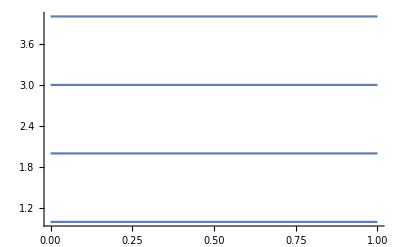

```mathematica
Plot[Table[x,{x,4}],{e,0,1}]
```

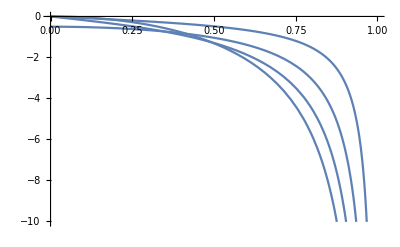

```mathematica
Plot[Re[Table[NpTwoC[e,n],{n,4}]],{e,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.70002}. NIntegrate obtained 3.1225×10^-17 + 3.4366×10^-13\ ⅈ and 8.65141×10^-16 for the integral and error estimates.

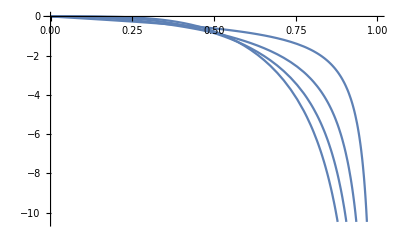

```mathematica
Plot[Re[Table[NpTwoD[e,n],{n,4}]],{e,0,1}]
```

So, yeah, I guess they’re not not partly real most of the time

## Shape of m=+2 feat. Ed Sheeran

```mathematica
Multicolumn[Flatten[{"p_(2, 1)","p_(2, 2)",Re[{With[{e=.1},NpPlus2[e,1]],With[{e=.1},NpPlus2[e,2]],With[{e=.5},NpPlus2[e,1]],With[{e=.5},NpPlus2[e,2]],With[{e=.9},NpPlus2[e,1]],With[{e=.9},NpPlus2[e,2]]}]}],4]
```

p_(2, 1) | -0.313767 | -1.52474 | -2.65957
p_(2, 2) | 6.12662 | 2.66301 | -3.61779

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

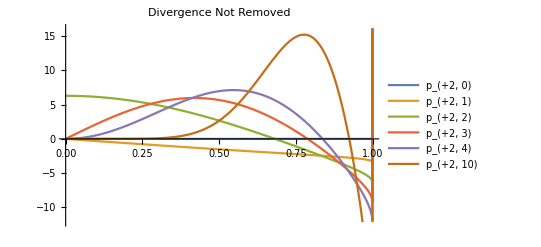

```mathematica
Plot[{Re[NpPlus2[e,0]],Re[NpPlus2[e,1]],Re[NpPlus2[e,2]],Re[NpPlus2[e,3]],Re[NpPlus2[e,4]],Re[NpPlus2[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)","p_(+2, 1)","p_(+2, 2)","p_(+2, 3)","p_(+2, 4)","p_(+2, 10)"},PlotLabel->"Divergence Not Removed"]
```

```mathematica
Limit[pPlus2[e,1],e->1,Direction->"FromBelow"]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^2 does not converge on {0, 2\ π}.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^4 does not converge on {0, 2\ π}.

$Aborted

```mathematica
Multicolumn[Flatten[{"p_(2, 1)","p_(2, 2)","p_(2, 3)",Re[{With[{e=.9},NpPlus2[e,1]],With[{e=.9},NpPlus2[e,2]],With[{e=.9},NpPlus2[e,3]],With[{e=.99},NpPlus2[e,1]],With[{e=.99},NpPlus2[e,2]],With[{e=.99},NpPlus2[e,3]],With[{e=.999},NpPlus2[e,1]],With[{e=.999},NpPlus2[e,2]],With[{e=.999},NpPlus2[e,3]],With[{e=.9999},NpPlus2[e,1]],With[{e=.9999},NpPlus2[e,2]],With[{e=.9999},NpPlus2[e,3]],With[{e=.99999},NpPlus2[e,1]],With[{e=.99999},NpPlus2[e,2]],With[{e=.99999},NpPlus2[e,3]],With[{e=.999999},NpPlus2[e,1]],With[{e=.999999},NpPlus2[e,2]],With[{e=.999999},NpPlus2[e,3]]}]}],7]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0192414}. NIntegrate obtained 3.69061×10^10 + 4.68329×10^7\ ⅈ and 2.21771×10^13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0192414}. NIntegrate obtained 1.8453×10^10 + 2.34169×10^7\ ⅈ and 1.10886×10^13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0192414}. NIntegrate obtained 3.69061×10^10 + 9.36657×10^7\ ⅈ and 2.21771×10^13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

p_(2, 1) | -2.65957 | -3.11682 | -3.28573 | -3.34483 | -3.36302 | 1.3884×10^15
p_(2, 2) | -3.61779 | -5.62128 | -6.1532 | -6.32247 | -6.37554 | 1.3884×10^15
p_(2, 3) | -3.78094 | -7.90384 | -8.9062 | -9.21271 | -9.30931 | 1.3884×10^15

```mathematica
Multicolumn[Flatten[{"p_(2, 1)/Pi","p_(2, 2)/2Pi","p_(2, 3)/3Pi",Re[{With[{e=.9999},NpPlus2[e,1]]/Pi,With[{e=.9999},NpPlus2[e,2]]/(2*Pi),With[{e=.9999},NpPlus2[e,3]]/(3*Pi)}]}],2]
```

p_(2, 1)/Pi | -1.06469
p_(2, 2)/2Pi | -1.00625
p_(2, 3)/3Pi | -0.977499

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

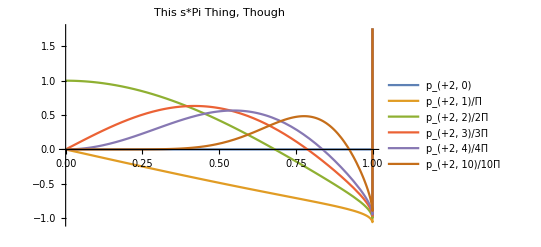

```mathematica
Plot[{Re[NpPlus2[e,0]],Re[NpPlus2[e,1]/Pi],Re[NpPlus2[e,2]/(2*Pi)],Re[NpPlus2[e,3]/(3*Pi)],Re[NpPlus2[e,4]/(4*Pi)],Re[NpPlus2[e,10]/(10*Pi)]},{e,0,1},PlotLegends->{"p_(+2, 0)","p_(+2, 1)/Π","p_(+2, 2)/2Π","p_(+2, 3)/3Π","p_(+2, 4)/4Π","p_(+2, 10)/10Π"},PlotLabel->"This s*Pi Thing, Though"]
```

```mathematica
With[{e=1},NpPlus2[e,2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained 9.08033×10^46 - 40.9123\ ⅈ and 6.72143×10^45 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained 4.30486×10^109 - 3.70411×10^62\ ⅈ and 8.18445×10^108 for the integral and error estimates.

NIntegrate::inumri: The integrand ⅇ^2\ ⅈ\ (u - Sin[u])\ Cos[2\ u]/(1 - Cos[u])^4 has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0., 1.35186×10^-14}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained -2.46151×10^94 + 2.42142×10^47\ ⅈ and 3.40473×10^93 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

9.08033×10^46-40.9123 ⅈ

```mathematica
With[{e=1},NpPlus2NP[e,2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained 9.08033×10^46 - 40.9123\ ⅈ and 6.72143×10^45 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained 4.30486×10^109 - 3.70411×10^62\ ⅈ and 8.18445×10^108 for the integral and error estimates.

NIntegrate::inumri: The integrand ⅇ^2\ ⅈ\ (u - Sin[u])\ Cos[2\ u]/(1 - Cos[u])^4 has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0., 1.35186×10^-14}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained -2.46151×10^94 + 2.42142×10^47\ ⅈ and 3.40473×10^93 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

0.+0. ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

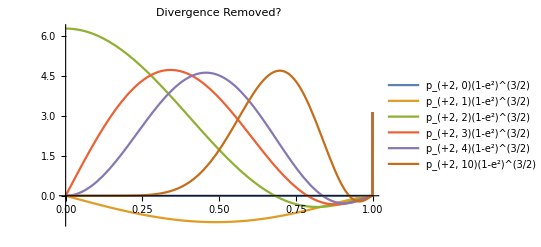

```mathematica
Plot[{Re[NpPlus2NP[e,0]],Re[NpPlus2NP[e,1]],Re[NpPlus2NP[e,2]],Re[NpPlus2NP[e,3]],Re[NpPlus2NP[e,4]],Re[NpPlus2NP[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)(1-e^2)^(3/2)","p_(+2, 1)(1-e^2)^(3/2)","p_(+2, 2)(1-e^2)^(3/2)","p_(+2, 3)(1-e^2)^(3/2)","p_(+2, 4)(1-e^2)^(3/2)","p_(+2, 10)(1-e^2)^(3/2)"},PlotLabel->"Divergence Removed?"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

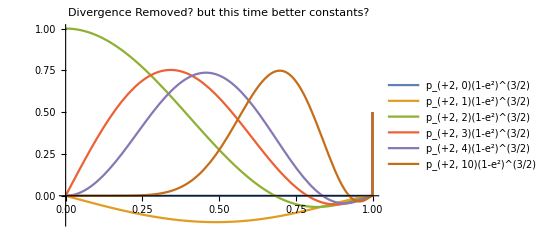

```mathematica
Plot[{Re[NpPlus2NP[e,0]],Re[NpPlus2NP[e,1]],Re[NpPlus2NP[e,2]],Re[NpPlus2NP[e,3]],Re[NpPlus2NP[e,4]],Re[NpPlus2NP[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)(1-e^2)^(3/2)","p_(+2, 1)(1-e^2)^(3/2)","p_(+2, 2)(1-e^2)^(3/2)","p_(+2, 3)(1-e^2)^(3/2)","p_(+2, 4)(1-e^2)^(3/2)","p_(+2, 10)(1-e^2)^(3/2)"},PlotLabel->"Divergence Removed? but this time better constants?"]
```

```mathematica
Limit[((1-e^2)^(3/2))*pPlus2[e,1],e->1,Direction->"FromBelow"]
```

```mathematica
Series[pPlus2[e,0]*((1-e^2)^(3/2)),{e,0,10}]
```

0

```mathematica
Series[pPlus2[e,1]*((1-e^2)^(3/2)),{e,0,10}]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^2 does not converge on {0, 2\ π}.

$Aborted

Attempt at Fourier series expansion:

```mathematica
FourierSeries[pPlus2NP[e,1],e,10]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^2 does not converge on {0, 2\ π}.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^4 does not converge on {0, 2\ π}.

$Aborted

#### Chebyshev

Attempt at Chebyshev series expansion:
http://www.cfm.brown.edu/people/dobrush/am34/Mathematica/ch5/chebyshev.html

These version’s didn’t work very well on a naive attempt, so I’m currently not focusing on them:

```mathematica
nc=Table[Re[2/π*Integrate[pPlus2NP[x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1}]],{n,0,5}]
```

$Aborted

```mathematica
cLtd=Table[Re[2/π*NIntegrate[NpPlus2NPLtd[x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1}]],{n,0,5}]
```

{-129751.,-129749.,-129747.,-129745.,-129745.,-129746.}

```mathematica
cWPLtd=Table[Re[2/π*NIntegrate[NpPlus2Ltd[x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1}]],{n,0,5}]
```

{-5.20537×10^26,-5.20537×10^26,-5.20537×10^26,-5.20537×10^26,-5.20537×10^26,-5.20537×10^26}

```mathematica
cWP=Table[Re[2/π*NIntegrate[NpPlus2[x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1}]],{n,0,5}]
```

{-5.20537×10^26,-5.20537×10^26,-5.20537×10^26,-5.20537×10^26,-5.20537×10^26,-5.20537×10^26}

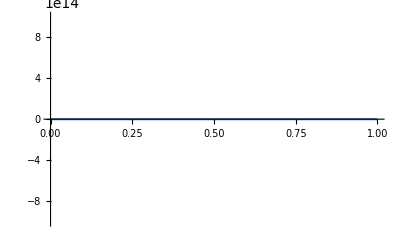

```mathematica
Plot[ {Re[NpPlus2[x,1]],-First[cWP]/2+Evaluate[cWP . Table[ChebyshevT[n-1,x],{n,Length[cWP]}]]},{x,0,1}]
```

This is the one I’ve been working with:

```mathematica
c=Table[Re[2/π*NIntegrate[NpPlus2NP[x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->5]],{n,0,5}]
```

NIntegrate::inumr: The integrand ⅇ^ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{-0.48329,-0.255691,0.165333,0.332489,0.156148,-0.0678808}

For the sake of n=5, I decreased PrecisionGoal from its default to 5 for all of them. Here’s how the changes play out:

```mathematica
{-0.4832902589281385,-0.2556905775177676,0.1653333350389714,0.3324886913980912,0.15614803960522897,-0.06788079608753599}
```

```mathematica
{-0.48329025130924647,-0.2556905683050831,0.16533333649625762,0.3324887012804893,0.1561480410420177,60933.49468438459}
```

It might be better to adjust the value for each n, but I’m going to do the lazy way first and see if that’s acceptable for our purposes

```mathematica
Re[2/π*NIntegrate[NpPlus2NP[x,1]*ChebyshevT[7,x]/(√(1-x^2)),{x,0,1,1},Exclusions->{1},PrecisionGoal->2,MaxRecursion->15]]
```

NIntegrate::inumr: The integrand ⅇ^ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

-0.00480681

I made it go even lower so that I could have more values of n

```mathematica
c=Table[Re[2/π*(NIntegrate[NpPlus2NP[x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->2]-NIntegrate[NpPlus2NP[-x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->2])],{n,0,10}]
```

NIntegrate::inumr: The integrand ⅇ^ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{0.,-0.511382,0.,0.664977,1.76697×10^-17,-0.135762,-1.76697×10^-17,-0.00961363,-3.53395×10^-17,-0.00400436,-8.83487×10^-18}

```mathematica
c[[Length[c]]]/129746
```

-0.999998

```mathematica
Last[c]
```

-129746.

```mathematica
-First[c]/2+Evaluate[c . Table[ChebyshevT[n-1,x],{n,Length[c]}]]
```

-0.241645-0.255691 x+0.165333 (-1+2 x^2)+0.332489 (-3 x+4 x^3)+0.156148 (1-8 x^2+8 x^4)-129746. (5 x-20 x^3+16 x^5)

```mathematica
-First[c]/2+Evaluate[c [[1;;5]]. Table[ChebyshevT[n-1,x],{n,Length[c]-1}]]
```

-0.241645-0.255691 x+0.165333 (-1+2 x^2)+0.332489 (-3 x+4 x^3)+0.156148 (1-8 x^2+8 x^4)

Agnostic of “good” parts of c:

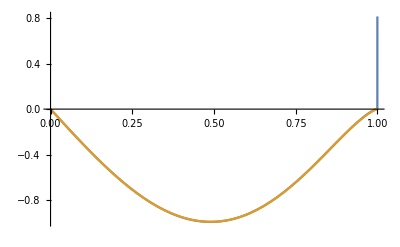

```mathematica
Plot[ {Re[NpPlus2NP[x,1]],-First[c]/2+Evaluate[c . Table[ChebyshevT[n-1,x],{n,Length[c]}]]},{x,0,1}]
```

Specialized for testing:

```mathematica
Plot[ {Re[NpPlus2NP[x,1]],-First[c]/2+Evaluate[c [[1;;5]]. Table[ChebyshevT[n-1,x],{n,Length[c]-1}]]},{x,0,1}]
```

```mathematica
c2=Table[Re[2/π*(NIntegrate[NpPlus2NP[x,2]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->1]+NIntegrate[NpPlus2NP[-x,2]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->1])],{n,0,10}]
```

NIntegrate::inumr: The integrand ⅇ^2\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^2\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{3.00103,-3.53395×10^-17,-2.78952,-2.82716×10^-16,1.64407,-2.82716×10^-16,-0.344168,0.,0.00092691,7.0679×10^-17,-0.0056138}

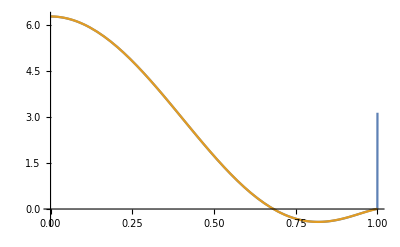

```mathematica
Plot[ {Re[NpPlus2NP[x,2]],-First[c2]/2+Evaluate[c2. Table[ChebyshevT[n-1,x],{n,Length[c2]}]]},{x,0,1}]
```

Pretend it goes to -1 (mirror image)

Okay, there’s also shifted Chebyshev polynomials that go from [0,1], so I’m going to try those. Don’t think that will remove the explosion problem, but it seems more honest.

```mathematica
shiftC=Table[Re[2/π*NIntegrate[NpPlus2NP[x,2]*ChebyshevT[n,2x-1]/(√(1-(2x-1)^2)),{x,0,1},PrecisionGoal->2]],{n,0,10}]
```

NIntegrate::inumr: The integrand ⅇ^2\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^2\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{2.56057,-1.87101,0.357463,0.334727,-0.0609851,-0.0314473,-0.00383087,-0.00163514,-0.00113804,-0.000702265,-0.000452841}

I tried to make these work for s=2, not knowing/being lazy about exactly how to find coefficients for the shifted versions may be hurting me here

```mathematica
-First[shiftC]/2+Evaluate[shiftC . Table[ChebyshevT[n-1,x],{n,Length[shiftC]}]]
```

-0.241645-129746. x+0.290407 (-1+2 x^2)-129746. (-3 x+4 x^3)-129746. (1-8 x^2+8 x^4)-129746. (5 x-20 x^3+16 x^5)

```mathematica
shiftC[[1]]/2+Evaluate[shiftC [[3]]*ChebyshevT[2,x]]
```

-0.241645+0.290407 (-1+2 x^2)

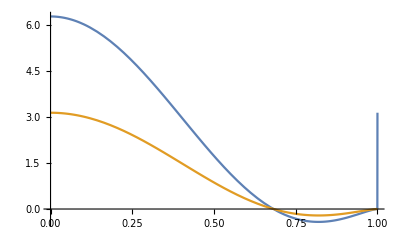

```mathematica
Plot[ {Re[NpPlus2NP[x,2]],-shiftC[[1]]/2+Evaluate[shiftC .Table[ChebyshevT[n-1,2x-1],{n,Length[shiftC]}]]},{x,0,1}]
```

```mathematica
c3=Table[Re[2/π*(NIntegrate[NpPlus2NP[x,3]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->2]-NIntegrate[NpPlus2NP[-x,3]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->2])],{n,0,10}]
```

NIntegrate::inumr: The integrand ⅇ^3\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^3\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{0.,1.05296,0.,-2.4778,-3.53395×10^-17,1.92512,0.,-0.512351,-2.12037×10^-16,0.0262391,0.}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {5.32588}. NIntegrate obtained 4.84522×10^-13 + 2.18575×10^-16\ ⅈ and 1.04604×10^-15 for the integral and error estimates.

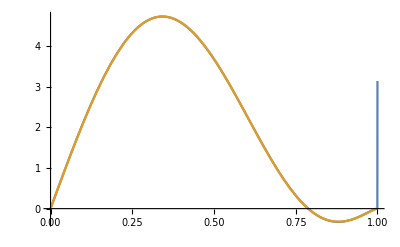

```mathematica
Plot[ {Re[NpPlus2NP[x,3]],-First[c3]/2+Evaluate[c3. Table[ChebyshevT[n-1,x],{n,Length[c3]}]]},{x,0,1}]
```

```mathematica
c100=Table[Re[2/π*(NIntegrate[NpPlus2NP[x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->1]-NIntegrate[NpPlus2NP[-x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->1])],{n,0,30}]
```

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999798140399496834140108639678325002485964872328549902}. NIntegrate obtained -1.04165×10^7 + 8.01075×10^7\ ⅈ and 1.92322×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.99999999999999798140399496834140108639678325002485964872328549902}. NIntegrate obtained 1.04165×10^7 - 8.01075×10^7\ ⅈ and 1.92322×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999798140399496834140108639678325002485964872328549902}. NIntegrate obtained -1.04165×10^7 + 8.01075×10^7\ ⅈ and 1.92322×10^8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{0.,1.23394,7.0679×10^-17,0.53724,0.,-0.403198,0.,-1.01452,7.0679×10^-17,-0.999685,7.0679×10^-17,-0.490285,-3.53395×10^-17,0.119342,-3.53395×10^-17,0.480449,-7.0679×10^-17,0.49098,3.53395×10^-17,0.278601,-1.76697×10^-17,0.042879,0.,-0.0897294,-7.0679×10^-17,-0.107133,-1.76697×10^-17,-0.0646282,2.65046×10^-17,-1.32627×10^7,0.}

```mathematica
c100[[2;;24;;2]]
```

{1.23395,0.537245,-0.403141,-1.01451,-0.999685,-0.490285,0.119342,0.480447,0.490981,0.278601,0.042879,-0.0897294}

```mathematica
c100[[2;;26]]
```

{1.23395,5.12539×10^-6,0.537245,5.15627×10^-6,-0.403141,5.13505×10^-6,-1.01451,4.79612×10^-6,-0.999685,7.0679×10^-17,-0.490285,-3.53395×10^-17,0.119342,-0.00183551,0.480447,5.55373×10^-7,0.490981,4.07215×10^-7,0.278601,-1.76697×10^-17,0.042879,-6.63137×10^6,-0.0897294,-0.466001,-6.63137×10^6}

```mathematica
Table[ChebyshevT[n-1,x],{n,2,Length[c100]-9,2}]
```

{x,-3 x+4 x^3,5 x-20 x^3+16 x^5,-7 x+56 x^3-112 x^5+64 x^7,9 x-120 x^3+432 x^5-576 x^7+256 x^9,-11 x+220 x^3-1232 x^5+2816 x^7-2816 x^9+1024 x^11,13 x-364 x^3+2912 x^5-9984 x^7+16640 x^9-13312 x^11+4096 x^13,-15 x+560 x^3-6048 x^5+28800 x^7-70400 x^9+92160 x^11-61440 x^13+16384 x^15,17 x-816 x^3+11424 x^5-71808 x^7+239360 x^9-452608 x^11+487424 x^13-278528 x^15+65536 x^17,-19 x+1140 x^3-20064 x^5+160512 x^7-695552 x^9+1770496 x^11-2723840 x^13+2490368 x^15-1245184 x^17+262144 x^19,21 x-1540 x^3+33264 x^5-329472 x^7+1793792 x^9-5870592 x^11+12042240 x^13-15597568 x^15+12386304 x^17-5505024 x^19+1048576 x^21}

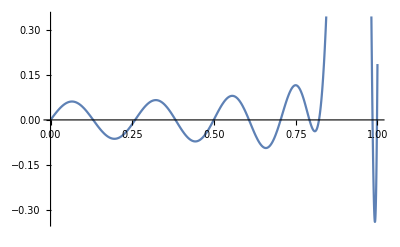

```mathematica
Plot[ {-First[c100]/2+Evaluate[c100[[2;;24;;2]]. Table[ChebyshevT[n-1,x],{n,2,Length[c100]-7,2}]]},{x,0,1},PlotRange->Automatic]
```

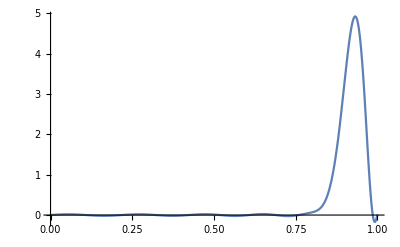

```mathematica
Plot[ {-First[c100]/2+Evaluate[c100[[1;;28]]. Table[ChebyshevT[n-1,x],{n,Length[c100]-3}]]},{x,0,1},PlotRange->Full]
```

```mathematica
c100
```

{0.,1.23394,7.0679×10^-17,0.53724,0.,-0.403198,0.,-1.01452,7.0679×10^-17,-0.999685,7.0679×10^-17,-0.490285,-3.53395×10^-17,0.119342,-3.53395×10^-17,0.480449,-7.0679×10^-17,0.49098,3.53395×10^-17,0.278601,-1.76697×10^-17,0.042879,0.,-0.0897294,-7.0679×10^-17,-0.107133,-1.76697×10^-17,-0.0646282,2.65046×10^-17,-1.32627×10^7,0.}

```mathematica
Plot[ {Evaluate[c100[[2;;28;;2]]. Table[ChebyshevT[n-1,x],{n,2,28,2}]]},{x,0,1},PlotRange->Full]
```

-Graphics-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {3.37475}. NIntegrate obtained 1.11673×10^-16 + 1.0018×10^-16\ ⅈ and 2.57131×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {3.37475}. NIntegrate obtained 1.97758×10^-16 - 6.31006×10^-17\ ⅈ and 4.13711×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853001364566677372607992192220043546624363983710281900130212}. NIntegrate obtained -2.94903×10^-17 - 2.76688×10^-16\ ⅈ and 7.92038×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

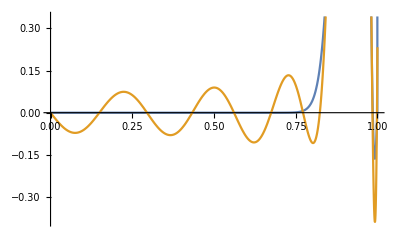

```mathematica
Plot[ {Re[NpPlus2NP[x,100]],-First[c100]/2+Evaluate[c100. Table[ChebyshevT[n-1,x],{n,Length[c100]}]]},{x,0,1}]
```

```mathematica
c100TakeTwo=Table[Re[2/π*(NIntegrate[NpPlus2NP[x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->1]+NIntegrate[NpPlus2NP[-x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->1])],{n,0,10}]
```

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{1.33364,-1.41358×10^-16,0.952234,0.,0.0593419,-3.53395×10^-17,-0.778448,-7.0679×10^-17,-1.0866,-1.41358×10^-16,-0.78473}

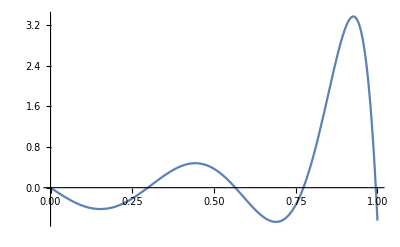

```mathematica
Plot[ {-First[c100]/2+Evaluate[c100[[1;;11]]. Table[ChebyshevT[n-1,x],{n,Length[c100TakeTwo[[1;;11]]]}]]},{x,0,1}]
```

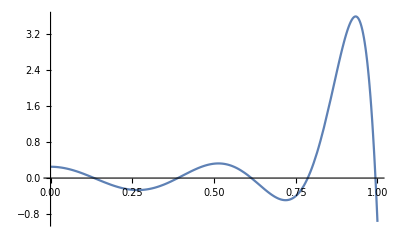

```mathematica
Plot[ {-First[c100TakeTwo]/2+Evaluate[c100TakeTwo. Table[ChebyshevT[n-1,x],{n,Length[c100TakeTwo]}]]} ,{x,0,1},PlotRange->Full]
```

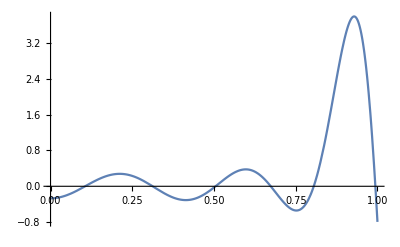

```mathematica
Plot[ {-First[c100TakeTwo]/2+Evaluate[c100TakeTwo. Table[ChebyshevT[n-1,x],{n,Length[c100TakeTwo]}]] + Evaluate[c100TakeTwob. Table[ChebyshevT[n-1,x],{n,12,16}]] },{x,0,1},PlotRange->Full]
```

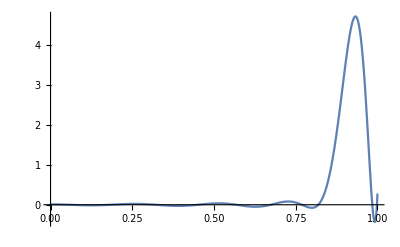

```mathematica
Plot[ {-First[c100TakeTwo]/2+Evaluate[c100TakeTwo. Table[ChebyshevT[n-1,x],{n,Length[c100TakeTwo]}]] + Evaluate[c100TakeTwob. Table[ChebyshevT[n-1,x],{n,12,16}]] +Evaluate[c100TakeTwoc. Table[ChebyshevT[n-1,x],{n,17,21}]] },{x,0,1},PlotRange->Full]
```

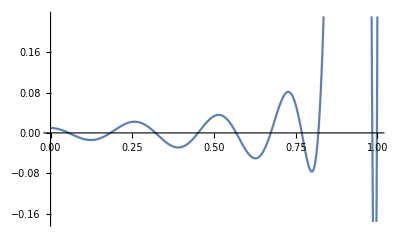

```mathematica
Plot[ {-First[c100TakeTwo]/2+Evaluate[Flatten[{c100TakeTwo,c100TakeTwob,c100TakeTwoc}]. Table[ChebyshevT[n-1,x],{n,21}]]},{x,0,1},PlotRange->Automatic]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {3.37475}. NIntegrate obtained 1.11673×10^-16 + 1.0018×10^-16\ ⅈ and 2.57131×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {3.37475}. NIntegrate obtained 1.97758×10^-16 - 6.31006×10^-17\ ⅈ and 4.13711×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853001364566677372607992192220043546624363983710281900130212}. NIntegrate obtained -2.94903×10^-17 - 2.76688×10^-16\ ⅈ and 7.92038×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

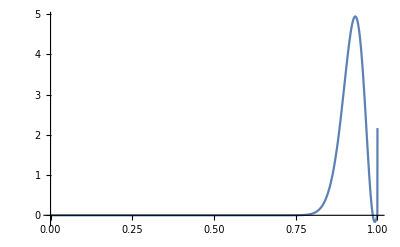

```mathematica
Plot[ {Re[NpPlus2NP[x,100]]},{x,0,1},PlotRange->Full]
```

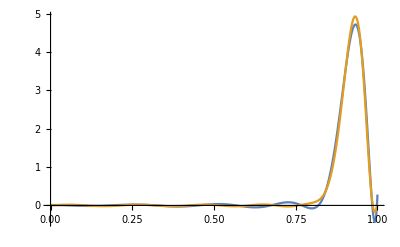

```mathematica
Plot[ {-First[c100Take3]/2+Evaluate[c100Take3. Table[ChebyshevT[n-1,x],{n,1,21,2}]],Evaluate[c100[[2;;28;;2]]. Table[ChebyshevT[n-1,x],{n,2,28,2}]]},{x,0,1},PlotRange->Full]
```

Whoops, guess take 1 was better after all. That makes sense intuitively, and from seeing that its first term is 0.

```mathematica
c100TakeTwob=Table[Re[2/π*(NIntegrate[NpPlus2NP[x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->1]+NIntegrate[NpPlus2NP[-x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->1])],{n,11,15}]
```

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{-1.06018×10^-16,-0.171758,0.,0.347633,3.53395×10^-17}

```mathematica
c100TakeTwoc=Table[Re[2/π*(NIntegrate[NpPlus2NP[x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->1]+NIntegrate[NpPlus2NP[-x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->1])],{n,16,20}]
```

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{0.525395,0.,0.399763,-1.76697×10^-17,0.152987}

```mathematica
Flatten[{c100TakeTwo,c100TakeTwob,c100TakeTwoc}]
```

{1.33364,-1.41358×10^-16,0.952234,0.,0.0593419,-3.53395×10^-17,-0.778448,-7.0679×10^-17,-1.0866,-1.41358×10^-16,-0.78473,-1.06018×10^-16,-0.171758,0.,0.347633,3.53395×10^-17,0.525395,0.,0.399763,-1.76697×10^-17,0.152987}

```mathematica
c100Take3=Table[Re[2/π*(NIntegrate[NpPlus2NP[x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->1]+NIntegrate[NpPlus2NP[-x,100]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->1])],{n,0,20,2}]
```

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^100\ ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{1.33364,0.952234,0.0593419,-0.778448,-1.0866,-0.78473,-0.171758,0.347633,0.525395,0.399763,0.152987}

### Just seeing how fast things go at different points

```mathematica
Plot[ {Re[NpPlus2NP[x,100]]},{x,0,.1},PlotRange->Full]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.76377}. NIntegrate obtained 1.77636×10^-15 + 3.62124×10^-16\ ⅈ and 7.67511×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.76377}. NIntegrate obtained 1.73646×10^-15 + 3.89988×10^-16\ ⅈ and 7.62176×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.76377}. NIntegrate obtained -1.84748×10^-16 + 6.80879×10^-17\ ⅈ and 5.09737×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

$Aborted

^ ~55 minutes

```mathematica
Plot[ {Re[NpPlus2NP[x,100]]},{x,.1,.2},PlotRange->Full]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853001364566677372607992192220043546624363983710281900130212}. NIntegrate obtained 1.81626×10^-15 - 1.23079×10^-15\ ⅈ and 1.32956×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853001364566677372607992192220043546624363983710281900130212}. NIntegrate obtained 1.21778×10^-15 - 1.52092×10^-15\ ⅈ and 1.54184×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853001364566677372607992192220043546624363983710281900130212}. NIntegrate obtained 2.22045×10^-16 + 1.6584×10^-15\ ⅈ and 1.39157×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

$Aborted

^ ~50 minutes

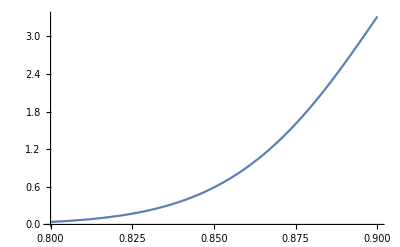

```mathematica
Plot[ {Re[NpPlus2NP[x,100]]},{x,.8,.9},PlotRange->Full]
```

^ ~1.5 minutes

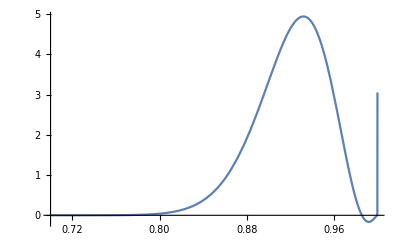

```mathematica
Plot[ {Re[NpPlus2NP[x,100]]},{x,.7,1},PlotRange->Full]
```

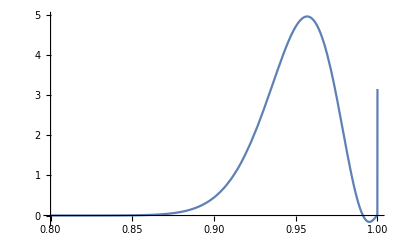

```mathematica
Plot[ {Re[NpPlus2NP[x,200]]},{x,.8,1},PlotRange->Full]
```

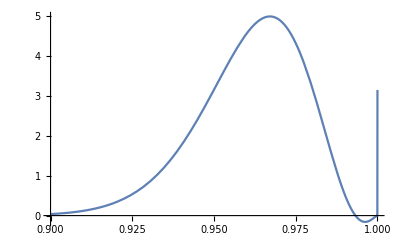

```mathematica
Plot[ {Re[NpPlus2NP[x,300]]},{x,.9,1},PlotRange->Full]
```

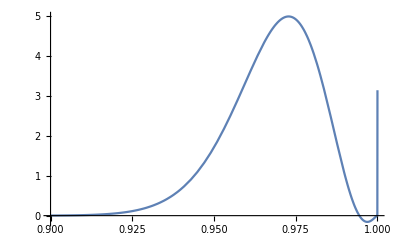

```mathematica
Plot[ {Re[NpPlus2NP[x,400]]},{x,.9,1},PlotRange->Full]
```

## Shape of m=-2 feat. Justin Bieber

```mathematica
Plot[{Re[NpMinus2[e,0]],Re[NpMinus2[e,1]],Re[NpMinus2[e,2]],Re[NpMinus2[e,3]],Re[NpMinus2[e,4]],Re[NpMinus2[e,10]]},{e,0,1},PlotLegends->{"p_(-2, 0)","p_(-2, 1)","p_(-2, 2)","p_(-2, 3)","p_(-2, 4)","p_(-2, 10)"},PlotLabel->"Divergence Not Removed"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

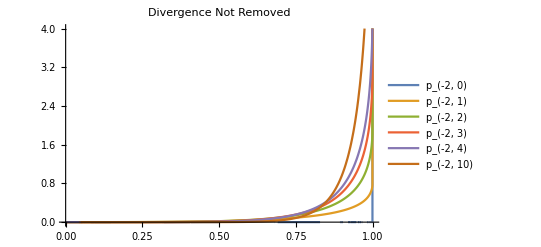

```mathematica
Plot[{Re[NpMinus2[e,0]],Re[NpMinus2[e,1]],Re[NpMinus2[e,2]],Re[NpMinus2[e,3]],Re[NpMinus2[e,4]],Re[NpMinus2[e,10]]},{e,0,1},PlotLegends->{"p_(-2, 0)","p_(-2, 1)","p_(-2, 2)","p_(-2, 3)","p_(-2, 4)","p_(-2, 10)"},PlotLabel->"Divergence Not Removed",PlotRange->{0,4}]
```

```mathematica
Multicolumn[Flatten[{"p_(-2, 1)","p_(-2, 2)","p_(-2, 3)",Re[{With[{e=.1},NpMinus2[e,1]],With[{e=.1},NpMinus2[e,2]],With[{e=.1},NpMinus2[e,3]],With[{e=.5},NpMinus2[e,1]],With[{e=.5},NpMinus2[e,2]],With[{e=.5},NpMinus2[e,3]],With[{e=.9},NpMinus2[e,1]],With[{e=.9},NpMinus2[e,2]],With[{e=.9},NpMinus2[e,3]],With[{e=.999},NpMinus2[e,1]],With[{e=.999},NpMinus2[e,2]],With[{e=.999},NpMinus2[e,3]],With[{e=.9999},NpMinus2[e,1]],With[{e=.9999},NpMinus2[e,2]],With[{e=.9999},NpMinus2[e,3]]}]}],6]
```

p_(-2, 1) | 0.000131806 | 0.0197906 | 0.233929 | 0.728321 | 0.787001
p_(-2, 2) | 0.0000263647 | 0.0199208 | 0.4513 | 1.73673 | 1.89759
p_(-2, 3) | 4.00106×10^-6 | 0.0148864 | 0.608663 | 2.78784 | 3.07296

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

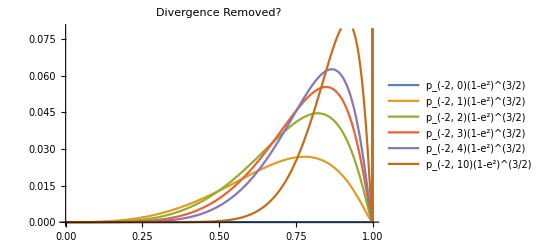

```mathematica
Plot[{Re[NpMinus2NP[e,0]],Re[NpMinus2NP[e,1]],Re[NpMinus2NP[e,2]],Re[NpMinus2NP[e,3]],Re[NpMinus2NP[e,4]],Re[NpMinus2NP[e,10]]},{e,0,1},PlotLegends->{"p_(-2, 0)(1-e^2)^(3/2)","p_(-2, 1)(1-e^2)^(3/2)","p_(-2, 2)(1-e^2)^(3/2)","p_(-2, 3)(1-e^2)^(3/2)","p_(-2, 4)(1-e^2)^(3/2)","p_(-2, 10)(1-e^2)^(3/2)"},PlotLabel->"Divergence Removed?",PlotRange->{0,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

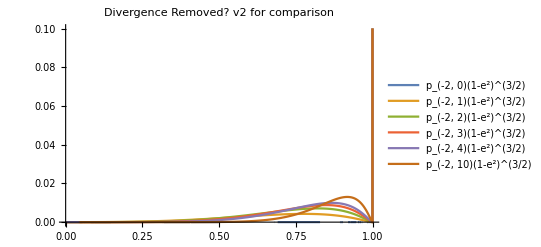

```mathematica
Plot[{Re[NpMinus2NP[e,0]],Re[NpMinus2NP[e,1]],Re[NpMinus2NP[e,2]],Re[NpMinus2NP[e,3]],Re[NpMinus2NP[e,4]],Re[NpMinus2NP[e,10]]},{e,0,1},PlotLegends->{"p_(-2, 0)(1-e^2)^(3/2)","p_(-2, 1)(1-e^2)^(3/2)","p_(-2, 2)(1-e^2)^(3/2)","p_(-2, 3)(1-e^2)^(3/2)","p_(-2, 4)(1-e^2)^(3/2)","p_(-2, 10)(1-e^2)^(3/2)"},PlotLabel->"Divergence Removed? v2 for comparison",PlotRange->{0,0.1}]
```

```mathematica
FullSimplify[p -2 0 or something]
```

```mathematica
Multicolumn[Flatten[{"p_(-2, 1)(1-e^2)^(3/2)","p_(-2, 2)(1-e^2)^(3/2)","p_(-2, 3)(1-e^2)^(3/2)",Re[{With[{e=.1},NpMinus2NP[e,1]],With[{e=.1},NpMinus2NP[e,2]],With[{e=.1},NpMinus2NP[e,3]],With[{e=.5},NpMinus2NP[e,1]],With[{e=.5},NpMinus2NP[e,2]],With[{e=.5},NpMinus2NP[e,3]],With[{e=.9},NpMinus2NP[e,1]],With[{e=.9},NpMinus2NP[e,2]],With[{e=.9},NpMinus2NP[e,3]],With[{e=.999},NpMinus2NP[e,1]],With[{e=.999},NpMinus2NP[e,2]],With[{e=.999},NpMinus2NP[e,3]],With[{e=.9999},NpMinus2NP[e,1]],With[{e=.9999},NpMinus2NP[e,2]],With[{e=.9999},NpMinus2NP[e,3]]}]}],6]
```

p_(-2, 1)(1-e^2)^(3/2) | 0.000129834 | 0.0128544 | 0.0193738 | 0.0000650942 | 2.22581×10^-6
p_(-2, 2)(1-e^2)^(3/2) | 0.0000259702 | 0.012939 | 0.0373762 | 0.000155221 | 5.36681×10^-6
p_(-2, 3)(1-e^2)^(3/2) | 3.94119×10^-6 | 0.00966901 | 0.0504089 | 0.000249165 | 8.69098×10^-6

It kind of looks like -2 is just going to be consistently smaller than +2; maybe even at its maximum value it’ll be negligible?
Except +2 is specifically small near e=1. But still. I guess with that in mind I don’t need to know the maximum, but it might dominate. I can do for both. Or something. Yeah.
At the very least it kind of looks like for low e, we can drop -2 basically entirely, and maybe drop both of them past some value s. Anyway.

```mathematica
FindMaximum[Limit[NpMinus2NP[e,s],s->Infinity],{e,.9}]
```

NIntegrate::inumr: The integrand ⅇ^ⅈ\ s\ (u - e\ Sin[u])/(1 - e\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^ⅈ\ s\ (u - e\ Sin[u])/(1 - e\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

$Aborted

And now, Chebyshev

```mathematica
mc=Table[Re[2/π*(NIntegrate[NpMinus2NP[x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,0,1},PrecisionGoal->2]-NIntegrate[NpMinus2NP[-x,1]*ChebyshevT[n,x]/(√(1-x^2)),{x,-1,0},PrecisionGoal->2])],{n,0,10}]
```

NIntegrate::inumr: The integrand ⅇ^ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^ⅈ\ (u - x\ Sin[u])/(1 - x\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{4.41744×10^-18,0.0172111,2.7609×10^-19,-0.00910847,1.10436×10^-18,-0.00925073,-2.7609×10^-19,0.0000163492,-8.28269×10^-19,0.000388757,0.}

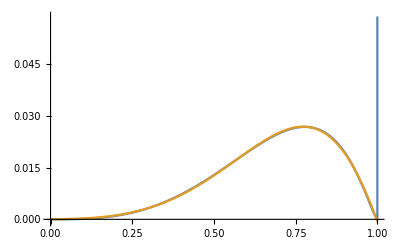

```mathematica
Plot[ {Re[NpMinus2NP[x,1]],-First[mc]/2+Evaluate[mc. Table[ChebyshevT[n-1,x],{n,Length[mc]}]]},{x,0,1}]
```